```mathematica
Animate[ParametricPlot[{If[t>0,y + y Erf[y/(2 √t)] + 2 √(t/π)Exp[-y^2/(4 t)],0],y},{y,-20,0},PlotRange -> {{0,6},All},AspectRatio -> 1,PlotStyle -> Thickness[0.01]],{t,-3,50}]
```

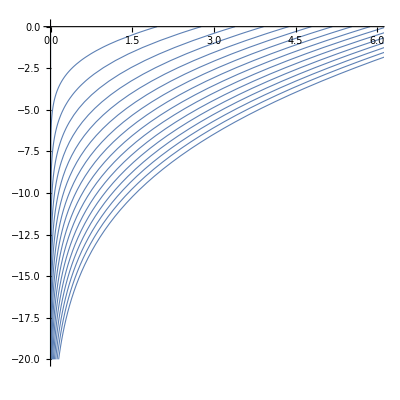

```mathematica
Show[Table[ParametricPlot[{If[t>0,y + y Erf[y/(2 √t)] + 2 √(t/π)Exp[-y^2/(4 t)],0],y},{y,-20,0},PlotRange -> {{0,6},All},AspectRatio -> 1,PlotStyle -> Thickness[0.002]],{t,0,50,3}]
]
```

```mathematica
Show[
ParametricPlot3D[{z,ⅇ^z Cos[z-π/4],ⅇ^z Sin[z-π/4]},{z,0,-3}],
Graphics3D[{Red,Table[Line[{{z,0,0},{z,ⅇ^z Cos[z-π/4],ⅇ^z Sin[z-π/4]}}],{z,0,-3,-.1}]}],
Graphics3D[Line[{{0,0,0},{-3,0,0}}]]
,PlotRange -> {{0,-3},{-1,1},{-1,1}}
]
```

-Graphics3D-